# GoIO a Wolfram Language device driver for the Go!Link USB sensor adapter by Vernier Software & Technology

## Installation

### Easy method

Download the latest release from github

Visit https://github.com/bobthechemist/goiolink/releases

Detailed instructions are provided on the release web page.

### DIY method

Clone the source repository and compile the driver yourself

Complete instructions are provided in the README file of the repository

https://github.com/bobthechemist/goiolink

## Basic Usage

### Load the package and open the device

```mathematica
<<GoIO`
dev = DeviceOpen["GoIO"]
```

```mathematica
DeviceObject[…]
```

The current version of the driver cannot be loaded twice.  Do not execute << GoIO` multiple times in the same kernel.

### Sensor readings can be obtained either by the Wolfram function DeviceRead or the “Read” property of the device driver.

```mathematica
DeviceRead["GoIO"]
```

24.9186

```mathematica
dev["Read"]
```

24.9161

### Device properties are more easily obtained through the device itself

```mathematica
dev["Properties"]
```

{Calibration,Name,Read,ReadAll,ReadLong,ReturnType,Units,ZZInitialized}

```mathematica
dev["Name"]
dev["Units"]
dev["ReadLong"]
```

```mathematica
Temperature
```

(C)

{24.9213,0.011394,999.}

### The “NativeProperties” of the device can be assigned values

```mathematica
dev["NativeProperties"]
```

{MeasurementPeriod}

```mathematica
dev["MeasurementPeriod"]
```

0.04

```mathematica
dev["MeasurementPeriod"]=1;
dev["MeasurementPeriod"]
```

1.

## Example Workflow

Load the package and open the device

```mathematica
<<GoIO`
dev = DeviceOpen["GoIO"]
```

```mathematica
DeviceObject[…]
```

Create an experiment.  The first argument is the time per point in seconds and the second argument is the number of points to collect.

```mathematica
expt = goioExperiment[0.5,10,"Title"-> "Example experiment", "Comment"->"Ambient temperature readings"]
```

ScheduledTaskObject[…]

Run the experiment - The message window will display “Done” when complete

```mathematica
StartScheduledTask[expt]
```

ScheduledTaskObject[…]

View the results of the experiment.  The argument is the experiment number and the function accepts the same options as DateListPlot

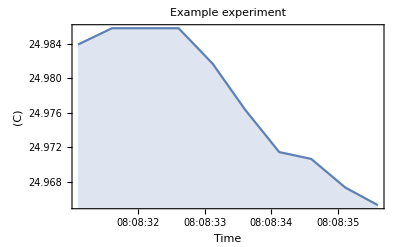

```mathematica
goioPlot[1,Filling->Axis]
```

Experiments are stored in a package symbol called $GoIOSessionData.  A summary of data currently stored can be obtained with goioDatatable[]

```mathematica
goioDataTable[]
```

Additional experiments can be run using the same process.  They will be automatically appended to the data table.

```mathematica
expt =  goioExperiment[0.5,10,"Title"-> "Second experiment", "Comment"->"More ambient temperature readings"];
StartScheduledTask[expt];
```

```mathematica
goioDataTable[]
```

Experiments are stored with actual time units.  To extract a list of x,y pairs with the x-axis in seconds, use goioDatalist

```mathematica
goioDataList[1]
```

{{0.,24.984},{0.509,24.986},{1.018,24.986},{1.508,24.986},{2.017,24.982},{2.506,24.976},{3.015,24.971},{3.504,24.971},{4.013,24.967},{4.502,24.965}}

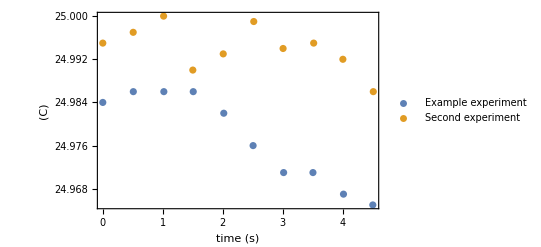

```mathematica
ListPlot[Map[goioDataList,{1,2}],
Frame->{True,True,False,False},FrameLabel->{"time (s)",Normal@goioDataTable[][1,"SensorUnits"]},PlotLegends->Values@Normal@goioDataTable[][All,"Title"]]
```

Session data can be stored with Save

```mathematica
Save["/home/pi/exampledata",$GoIOSessionData]
```

Retreiving this data will overwrite any results currently in $GoIOSessionData, but can be used to, for example, start where you left off.

```mathematica
Get["/home/pi/exampledata"];
goioDataTable[]
```